◼"◼"◼"◼"2021-03-17T21:48:59v0.00◼"◼"M. J. Steil[msteil@theorie.ikp.physik.tu-darmstadt.de](mailto:msteil@theorie.ikp.physik.tu-darmstadt.de)TU Darmstadt

# Reference integrals for n-dimensional integration

Martin Jakob Steil^1

^1Technische Universität Darmstadt

Reference integrals for unit tests of n-dimensional integration routines (cubature_function.hpp)

Initialization

```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];

(** Git setup **)

(* Disable Notebookhistory, [https://mathematica.stackexchange.com/questions/11258/are-there-suitable-versioning-systems-for-mathematica-notebooks]*)
SetOptions[EvaluationNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},System`TrackCellChangeTimes->False]

(* Display the Timing of an Evaluation in a Notebook Window [https://reference.wolfram.com/language/howto/DisplayTheTimingOfAnEvaluationInANotebookWindow.html] *)
SetOptions[EvaluationNotebook[],EvaluationCompletionAction->{"ShowTiming"}]
```

## Generic test integrals

## One dimensional tests

```mathematica
f1=Integrate[Log[x^4]Exp[-x^2],x]
f2=Integrate[Exp[-a x^2],x,Assumptions->a>0]
```

-4 x HypergeometricPFQ[{1/2,1/2},{3/2,3/2},-x^2]+1/2 √π Erf[x] Log[x^4]

(√π Erf[√a x])/(2 √a)

```mathematica
N[Limit[f1,x->#[[2]]]-Limit[f1,x->#[[1]]]&@{0,1},32]//CForm
```

-3.6237619052894513551968719596309

```mathematica
N[Limit[f1,x->#[[2]]]-Limit[f1,x->#[[1]]]&@{-2,∞},32]//CForm
```

-6.9735446427682748703903289486457

```mathematica
N[Limit[f1,x->#[[2]]]-Limit[f1,x->#[[1]]]&@{-∞,π},32]//CForm
```

-6.9604992352619167721204516151225

```mathematica
N[Limit[f2,x->#[[2]]]-Limit[f2,x->#[[1]]]&@{-∞,∞},32]/.a->2//CForm
```

1.2533141373155002512078826424055

## Two dimensional tests

```mathematica
Integrate[Exp[-x^2-y^4],{x,-1,1},{y,1,Infinity}]
N[%,32]//CForm
```

1/4 √π Erf[1] Gamma[1/4,1]

0.09195478602009999018458155633008

## Complex test

```mathematica
Integrate[1/(x+1+I ϵ),{x,0,1},Assumptions->ϵ>0]
%/.ϵ->1/10.;
N[%,32]//CForm
```

-Log[1+ⅈ ϵ]+Log[2+ⅈ ϵ]

Complex(0.6894204552326549,-0.04971025676921927)

{Re[1/((1+ⅈ/10)+x)],Im[1/((1+ⅈ/10)+x)]}

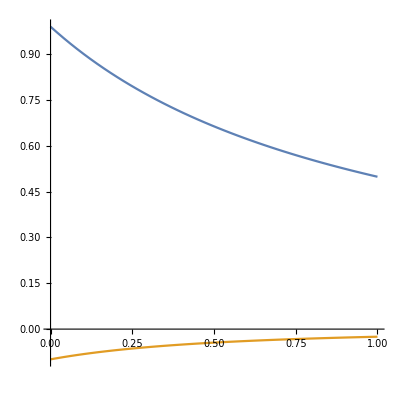

{0.332963,-0.0110988}

```mathematica
1/(x+1+I ϵ)/.ϵ->1/10;
{Re[%],Im[%]}
Plot[%,{x,0,1},PlotRange->All,AspectRatio->1]
%%/.x->2.
```